```mathematica
bp[l_,h_,fs_,n_]:=Module[{nyq=fs/2},
LeastSquaresFilterKernel[{"Bandpass",{(l/nyq)*Pi,(h/nyq)*Pi}},n]
]
```

```mathematica
lp[h_,fs_,n_]:=Module[{nyq=fs/2},
LeastSquaresFilterKernel[{"Lowpass",(h/nyq)*Pi},n]
]
```

```mathematica
cos[f_,fs_,nsec_]:=Table[Cos[2*Pi*f*t],{t,0,nsec,1/fs}]
```

```mathematica
addnoise[dat_]:=Table[dat[[i]]+RandomReal[{-1.,1.}],{i,1,Length[dat]}]
```

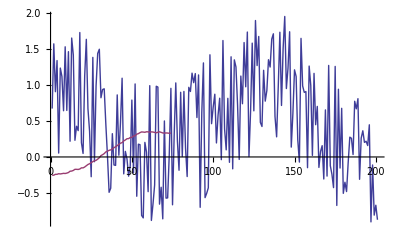
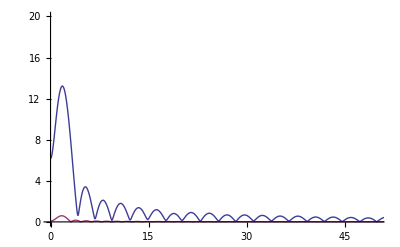

```mathematica
Module[
{dat = addnoise[cos[1.5,200,1]*.5+.5],
filt=bp[1,2,200,128]
},
{
ListLinePlot[{dat,ListConvolve[filt,dat]}],
Plot[{Abs[ListFourierSequenceTransform[ListConvolve[filt,dat],(x/100)*Pi]],Abs[ListFourierSequenceTransform[filt,(x/100)*Pi]]},{x,0,200},PlotRange->{{0.,50},{0.,20}}]
}
]
```

```mathematica
Module[{filt=bp[5,15,200,65]},{Table[ToString[NumberForm[filt[[i]],ExponentFunction->(Null&)]],{i,1,Length[filt]}]}]
```

{{0.0153071,0.0192906,0.0212207,0.0206209,0.0174939,0.0123485,0.00612134,-0.0000000000000000127222,-0.00481803,-0.00738614,-0.00723432,-0.00451024,0.00000000000000000389817,0.004985,0.00884194,0.00999302,0.00722705,-0.00000000000000000471193,-0.0113682,-0.025647,-0.040819,-0.0543643,-0.063662,-0.0664452,-0.0612286,-0.0476301,-0.0265258,0.0000000000000000070679,0.0289082,0.0566271,0.0795775,0.094715,0.1,0.094715,0.0795775,0.0566271,0.0289082,0.0000000000000000070679,-0.0265258,-0.0476301,-0.0612286,-0.0664452,-0.063662,-0.0543643,-0.040819,-0.025647,-0.0113682,-0.00000000000000000471193,0.00722705,0.00999302,0.00884194,0.004985,0.00000000000000000389817,-0.00451024,-0.00723432,-0.00738614,-0.00481803,-0.0000000000000000127222,0.00612134,0.0123485,0.0174939,0.0206209,0.0212207,0.0192906,0.0153071}}

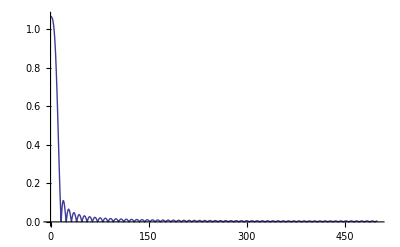

```mathematica
Plot[Abs[ListFourierSequenceTransform[lp, Pi*(x/500)]], {x, 0, 500},PlotRange->Full]
```

```mathematica
makefilters[nfilters_,ntaps_,fs_]:=
Module[{nyq=fs/2,width=(fs/2)/nfilters},
Flatten[{{LeastSquaresFilterKernel[{"Lowpass",(width/nyq)*Pi},ntaps]},
Table[LeastSquaresFilterKernel[{"Bandpass",{((i*width)/nyq)*Pi,(((i+1)*width)/nyq)*Pi}},ntaps],{i,1,nfilters-2}],
{LeastSquaresFilterKernel[{"Highpass",Pi-(width/nyq)*Pi},ntaps]}},1]]
```

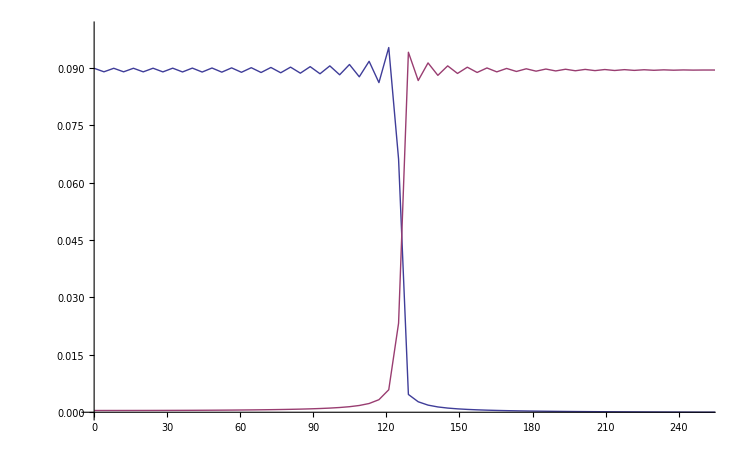

```mathematica
ListLinePlot[Map[Function[l,Abs[Fourier[l]]],makefilters[2,125,500]],PlotRange->{{0,250},{0,.1}},DataRange->{0,500}]
```

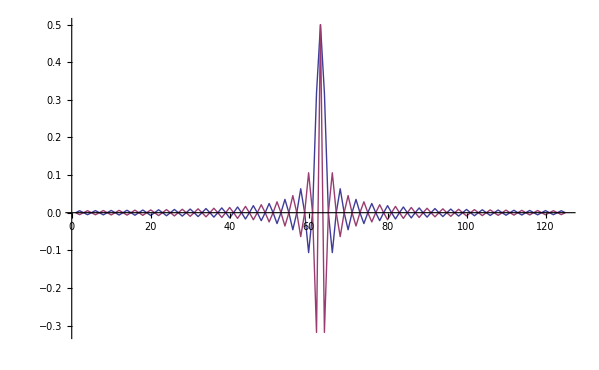

```mathematica
ListLinePlot[makefilters[2,125,500],PlotRange->Full]
```

```mathematica
fmt[filters_]:=
Module[{txt="/nfilters : "<>ToString[Length[filters]]<>",/filter/description : ["},
For[i=1,i<=Length[filters],i++,
txt=txt<>"{/channel/number : "<>ToString[NumberForm[i-1,ExponentFunction->(Null&)]]<>",/coefficients : [";
For[j=1,j<=Length[filters[[i]]],j++,
txt=txt<>ToString[NumberForm[filters[[i]][[j]],ExponentFunction->(Null&)]];
If[j<Length[filters[[i]]],txt=txt<>","]];
txt=txt<>"]}";
If[i<Length[filters],txt=txt<>","]];
txt<>"]"]
```

```mathematica
fmt[makefilters[32,128,200]]
```

/nfilters : 32,/filter/description : [{/channel/number : 0,/coefficients : [-0.000245964,-0.000747292,-0.00125761,-0.00177249,-0.00228731,-0.00279733,-0.00329769,-0.00378343,-0.00424959,-0.00469117,-0.00510324,-0.00548093,-0.00581947,-0.00611427,-0.0063609,-0.00655518,-0.00669319,-0.00677128,-0.00678617,-0.00673489,-0.00661491,-0.00642408,-0.0061607,-0.00582351,-0.00541174,-0.00492512,-0.00436384,-0.00372863,-0.00302071,-0.00224183,-0.0013942,-0.000480576,0.000495833,0.00153134,0.0026218,0.00376264,0.00494891,0.00617524,0.00743596,0.00872506,0.0100363,0.0113631,0.0126988,0.0140365,0.0153694,0.0166903,0.0179923,0.0192683,0.0205114,0.0217148,0.0228719,0.0239762,0.0250216,0.0260022,0.0269125,0.0277473,0.0285018,0.0291718,0.0297535,0.0302433,0.0306387,0.0309372,0.0311372,0.0312375,0.0312375,0.0311372,0.0309372,0.0306387,0.0302433,0.0297535,0.0291718,0.0285018,0.0277473,0.0269125,0.0260022,0.0250216,0.0239762,0.0228719,0.0217148,0.0205114,0.0192683,0.0179923,0.0166903,0.0153694,0.0140365,0.0126988,0.0113631,0.0100363,0.00872506,0.00743596,0.00617524,0.00494891,0.00376264,0.0026218,0.00153134,0.000495833,-0.000480576,-0.0013942,-0.00224183,-0.00302071,-0.00372863,-0.00436384,-0.00492512,-0.00541174,-0.00582351,-0.0061607,-0.00642408,-0.00661491,-0.00673489,-0.00678617,-0.00677128,-0.00669319,-0.00655518,-0.0063609,-0.00611427,-0.00581947,-0.00548093,-0.00510324,-0.00469117,-0.00424959,-0.00378343,-0.00329769,-0.00279733,-0.00228731,-0.00177249,-0.00125761,-0.000747292,-0.000245964]},{/channel/number : 1,/coefficients : [-0.000245372,-0.000731116,-0.00118223,-0.00156526,-0.0018481,-0.00200137,-0.00199977,-0.00182324,-0.00145811,-0.000897884,-0.000143939,0.000794131,0.00189843,0.00314298,0.00449423,0.00591189,0.00735003,0.00875839,0.010084,0.0112727,0.0122714,0.0130294,0.0135005,0.0136452,0.0134314,0.0128369,0.0118498,0.0104699,0.00870899,0.00659111,0.00415243,0.00144057,-0.0014863,-0.00456086,-0.00770825,-0.010848,-0.0138964,-0.0167686,-0.0193812,-0.0216547,-0.0235161,-0.024901,-0.0257557,-0.0260393,-0.0257249,-0.0248011,-0.0232723,-0.0211592,-0.0184985,-0.0153424,-0.0117571,-0.00782153,-0.00362538,0.000733406,0.00515102,0.0095206,0.0137351,0.0176902,0.0212873,0.024436,0.0270567,0.0290829,0.0304631,0.0311622,0.0311622,0.0304631,0.0290829,0.0270567,0.024436,0.0212873,0.0176902,0.0137351,0.0095206,0.00515102,0.000733406,-0.00362538,-0.00782153,-0.0117571,-0.0153424,-0.0184985,-0.0211592,-0.0232723,-0.0248011,-0.0257249,-0.0260393,-0.0257557,-0.024901,-0.0235161,-0.0216547,-0.0193812,-0.0167686,-0.0138964,-0.010848,-0.00770825,-0.00456086,-0.0014863,0.00144057,0.00415243,0.00659111,0.00870899,0.0104699,0.0118498,0.0128369,0.0134314,0.0136452,0.0135005,0.0130294,0.0122714,0.0112727,0.010084,0.00875839,0.00735003,0.00591189,0.00449423,0.00314298,0.00189843,0.000794131,-0.000143939,-0.000897884,-0.00145811,-0.00182324,-0.00199977,-0.00200137,-0.0018481,-0.00156526,-0.00118223,-0.000731116,-0.000245372]},{/channel/number : 2,/coefficients : [-0.000244188,-0.000699112,-0.00103599,-0.00117504,-0.00105401,-0.000635935,0.000085231,0.00108156,0.00229117,0.00362143,0.00495524,0.00616,0.00709859,0.00764163,0.00767978,0.00713535,0.00597189,0.00420104,0.00188575,-0.000860442,-0.00387848,-0.00697278,-0.00992383,-0.0125036,-0.0144923,-0.0156963,-0.015964,-0.0152008,-0.0133791,-0.0105453,-0.00682076,-0.00239709,0.00247319,0.00749166,0.0123327,0.0166652,0.0201755,0.0225906,0.0236983,0.0233651,0.0215487,0.018304,0.0137834,0.00822995,0.00196357,-0.00463794,-0.0111628,-0.0171918,-0.0223267,-0.0262172,-0.0285854,-0.0292462,-0.0281217,-0.0252481,-0.0207756,-0.01496,-0.00814777,-0.000753967,0.00676404,0.0139364,0.0203114,0.0254854,0.0291297,0.0310119,0.0310119,0.0291297,0.0254854,0.0203114,0.0139364,0.00676404,-0.000753967,-0.00814777,-0.01496,-0.0207756,-0.0252481,-0.0281217,-0.0292462,-0.0285854,-0.0262172,-0.0223267,-0.0171918,-0.0111628,-0.00463794,0.00196357,0.00822995,0.0137834,0.018304,0.0215487,0.0233651,0.0236983,0.0225906,0.0201755,0.0166652,0.0123327,0.00749166,0.00247319,-0.00239709,-0.00682076,-0.0105453,-0.0133791,-0.0152008,-0.015964,-0.0156963,-0.0144923,-0.0125036,-0.00992383,-0.00697278,-0.00387848,-0.000860442,0.00188575,0.00420104,0.00597189,0.00713535,0.00767978,0.00764163,0.00709859,0.00616,0.00495524,0.00362143,0.00229117,0.00108156,0.000085231,-0.000635935,-0.00105401,-0.00117504,-0.00103599,-0.000699112,-0.000244188]},{/channel/number : 3,/coefficients : [-0.000242416,-0.000651976,-0.000827661,-0.000647441,-0.0000575313,0.000910452,0.00213668,0.00342601,0.00453543,0.00521246,0.00523895,0.00447335,0.00288446,0.000570553,-0.00224051,-0.00521166,-0.00793608,-0.00999123,-0.0110004,-0.010693,-0.00895487,-0.00585991,-0.0016773,0.00314859,0.00804476,0.0123778,0.0155358,0.0170127,0.016485,0.0138675,0.00934145,0.00334784,-0.00345413,-0.0102603,-0.0162179,-0.0205339,-0.0225805,-0.0219846,-0.0186881,-0.0129701,-0.00542629,0.00309369,0.0115835,0.0190018,0.0244019,0.027055,0.0265481,0.0228463,0.0163075,0.00764864,-0.00213429,-0.011884,-0.0204218,-0.0266937,-0.029903,-0.0296137,-0.0258093,-0.0189014,-0.0096839,0.000760692,0.0111915,0.0203605,0.0271657,0.0307868,0.0307868,0.0271657,0.0203605,0.0111915,0.000760692,-0.0096839,-0.0189014,-0.0258093,-0.0296137,-0.029903,-0.0266937,-0.0204218,-0.011884,-0.00213429,0.00764864,0.0163075,0.0228463,0.0265481,0.027055,0.0244019,0.0190018,0.0115835,0.00309369,-0.00542629,-0.0129701,-0.0186881,-0.0219846,-0.0225805,-0.0205339,-0.0162179,-0.0102603,-0.00345413,0.00334784,0.00934145,0.0138675,0.016485,0.0170127,0.0155358,0.0123778,0.00804476,0.00314859,-0.0016773,-0.00585991,-0.00895487,-0.010693,-0.0110004,-0.00999123,-0.00793608,-0.00521166,-0.00224051,0.000570553,0.00288446,0.00447335,0.00523895,0.00521246,0.00453543,0.00342601,0.00213668,0.000910452,-0.0000575313,-0.000647441,-0.000827661,-0.000651976,-0.000242416]},{/channel/number : 4,/coefficients : [-0.00024006,-0.000590726,-0.00056972,-0.0000441489,0.000949996,0.00219778,0.00334717,0.00399545,0.00380044,0.00258868,0.000431472,-0.00233479,-0.0051551,-0.00736436,-0.00833728,-0.0076468,-0.00519308,-0.001269,0.00345999,0.00806516,0.0115359,0.012998,0.0119222,0.00827463,0.00257075,-0.00418766,-0.0106869,-0.0155579,-0.0176636,-0.0163585,-0.0116599,-0.00429053,0.00442674,0.0128068,0.0191311,0.022002,0.0206495,0.015123,0.00632254,-0.00414469,-0.0142605,-0.0219898,-0.0256937,-0.0244786,-0.0184051,-0.00850971,0.00337192,0.0149498,0.0239271,0.0284618,0.0275482,0.021239,0.0106588,-0.00219845,-0.0148508,-0.0248146,-0.0300991,-0.0296096,-0.0233764,-0.0125611,0.000763146,0.0140151,0.0246136,0.0304876,0.0304876,0.0246136,0.0140151,0.000763146,-0.0125611,-0.0233764,-0.0296096,-0.0300991,-0.0248146,-0.0148508,-0.00219845,0.0106588,0.021239,0.0275482,0.0284618,0.0239271,0.0149498,0.00337192,-0.00850971,-0.0184051,-0.0244786,-0.0256937,-0.0219898,-0.0142605,-0.00414469,0.00632254,0.015123,0.0206495,0.022002,0.0191311,0.0128068,0.00442674,-0.00429053,-0.0116599,-0.0163585,-0.0176636,-0.0155579,-0.0106869,-0.00418766,0.00257075,0.00827463,0.0119222,0.012998,0.0115359,0.00806516,0.00345999,-0.001269,-0.00519308,-0.0076468,-0.00833728,-0.00736436,-0.0051551,-0.00233479,0.000431472,0.00258868,0.00380044,0.00399545,0.00334717,0.00219778,0.000949996,-0.0000441489,-0.00056972,-0.000590726,-0.00024006]},{/channel/number : 5,/coefficients : [-0.000237126,-0.000516688,-0.000277632,0.000564304,0.0017751,0.00285974,0.00324026,0.00249486,0.00056901,-0.00212831,-0.00479531,-0.00646985,-0.00635786,-0.00414934,-0.000206158,0.00446124,0.00844571,0.0103636,0.00931896,0.00525884,-0.00090958,-0.00750467,-0.0125267,-0.0142624,-0.0118544,-0.00565071,0.00279721,0.0111156,0.0167772,0.017869,0.013726,0.00522288,-0.00538868,-0.0150761,-0.0208976,-0.0208979,-0.0147534,-0.00395831,0.00853147,0.0191121,0.0245799,0.0231049,0.0148348,0.00193008,-0.0120009,-0.0229196,-0.0275377,-0.0243134,-0.0139594,0.000703779,0.0155216,0.0261944,0.0295363,0.0244332,0.0122098,-0.0037153,-0.0187946,-0.0286638,-0.0304172,-0.0234708,-0.0097544,0.00682974,0.0215287,0.030115,0.030115,0.0215287,0.00682974,-0.0097544,-0.0234708,-0.0304172,-0.0286638,-0.0187946,-0.0037153,0.0122098,0.0244332,0.0295363,0.0261944,0.0155216,0.000703779,-0.0139594,-0.0243134,-0.0275377,-0.0229196,-0.0120009,0.00193008,0.0148348,0.0231049,0.0245799,0.0191121,0.00853147,-0.00395831,-0.0147534,-0.0208979,-0.0208976,-0.0150761,-0.00538868,0.00522288,0.013726,0.017869,0.0167772,0.0111156,0.00279721,-0.00565071,-0.0118544,-0.0142624,-0.0125267,-0.00750467,-0.00090958,0.00525884,0.00931896,0.0103636,0.00844571,0.00446124,-0.000206158,-0.00414934,-0.00635786,-0.00646985,-0.00479531,-0.00212831,0.00056901,0.00249486,0.00324026,0.00285974,0.0017751,0.000564304,-0.000277632,-0.000516688,-0.000237126]},{/channel/number : 6,/coefficients : [-0.00023362,-0.000431466,0.0000310972,0.00110678,0.00225935,0.00270799,0.00185803,-0.000298316,-0.00303619,-0.00512434,-0.00536203,-0.00319764,0.000871305,0.00534795,0.00827678,0.0080846,0.00436426,-0.00177232,-0.00798864,-0.0116085,-0.0107581,-0.00528163,0.00300218,0.0108814,0.0149963,0.013265,0.00588845,-0.00453888,-0.0139292,-0.0183085,-0.0154949,-0.00614264,0.00633765,0.017019,0.0214116,0.0173505,0.00602433,-0.00833271,-0.0200276,-0.0241776,-0.0187531,-0.00553736,0.0104404,0.0228281,0.0264911,0.0196477,0.00470931,-0.0125638,-0.025297,-0.0282552,-0.0200053,-0.00358978,0.0145979,0.0273208,0.0293975,0.0198245,0.00224731,-0.0164364,-0.0288031,-0.0298737,-0.0191315,-0.00076499,0.0179778,0.0296698,0.0296698,0.0179778,-0.00076499,-0.0191315,-0.0298737,-0.0288031,-0.0164364,0.00224731,0.0198245,0.0293975,0.0273208,0.0145979,-0.00358978,-0.0200053,-0.0282552,-0.025297,-0.0125638,0.00470931,0.0196477,0.0264911,0.0228281,0.0104404,-0.00553736,-0.0187531,-0.0241776,-0.0200276,-0.00833271,0.00602433,0.0173505,0.0214116,0.017019,0.00633765,-0.00614264,-0.0154949,-0.0183085,-0.0139292,-0.00453888,0.00588845,0.013265,0.0149963,0.0108814,0.00300218,-0.00528163,-0.0107581,-0.0116085,-0.00798864,-0.00177232,0.00436426,0.0080846,0.00827678,0.00534795,0.000871305,-0.00319764,-0.00536203,-0.00512434,-0.00303619,-0.000298316,0.00185803,0.00270799,0.00225935,0.00110678,0.0000310972,-0.000431466,-0.00023362]},{/channel/number : 7,/coefficients : [-0.000229552,-0.000336904,0.000337962,0.00151987,0.00230976,0.00178569,-0.000255488,-0.00293693,-0.00464697,-0.00397683,-0.000717964,0.00373552,0.00694493,0.00674823,0.00263507,-0.00366785,-0.00887399,-0.00984353,-0.0054368,0.0025627,0.0101089,0.0129353,0.00894995,-0.000352669,-0.0103686,-0.0156585,-0.0128986,-0.0029094,0.00945284,0.0176506,0.0169285,0.00704761,-0.00727134,-0.0185936,-0.0206422,-0.0117746,0.00386157,0.0182527,0.0236412,0.0167168,0.000607791,-0.0165077,-0.0255697,-0.0214507,-0.00584821,0.0133716,0.0261557,0.0255463,0.0114768,-0.00899559,-0.0252434,-0.0286131,-0.0170534,0.0036582,0.0228144,0.030342,0.0221249,0.00226008,-0.0189933,-0.0305401,-0.026272,-0.00831387,0.0140377,0.0291531,0.0291531,0.0140377,-0.00831387,-0.026272,-0.0305401,-0.0189933,0.00226008,0.0221249,0.030342,0.0228144,0.0036582,-0.0170534,-0.0286131,-0.0252434,-0.00899559,0.0114768,0.0255463,0.0261557,0.0133716,-0.00584821,-0.0214507,-0.0255697,-0.0165077,0.000607791,0.0167168,0.0236412,0.0182527,0.00386157,-0.0117746,-0.0206422,-0.0185936,-0.00727134,0.00704761,0.0169285,0.0176506,0.00945284,-0.0029094,-0.0128986,-0.0156585,-0.0103686,-0.000352669,0.00894995,0.0129353,0.0101089,0.0025627,-0.0054368,-0.00984353,-0.00887399,-0.00366785,0.00263507,0.00674823,0.00694493,0.00373552,-0.000717964,-0.00397683,-0.00464697,-0.00293693,-0.000255488,0.00178569,0.00230976,0.00151987,0.000337962,-0.000336904,-0.000229552]},{/channel/number : 8,/coefficients : [-0.000224931,-0.000235049,0.000624571,0.00175526,0.00191664,0.000355294,-0.00226845,-0.00405393,-0.00320524,0.000386358,0.00462382,0.00639192,0.00380805,-0.00206857,-0.00750349,-0.00844455,-0.00349341,0.00466101,0.0106307,0.00988176,0.00211384,-0.00801849,-0.0136651,-0.0104078,0.000369027,0.0118889,0.0162385,0.00979901,-0.00387129,-0.0159348,-0.0179955,-0.0079356,0.00818752,0.0197656,0.0186356,0.00482213,-0.013006,-0.022979,-0.01795,-0.000594961,0.0179368,0.0252046,0.0158505,-0.00448546,-0.0225507,-0.0261458,-0.012385,0.0100568,0.0264233,0.0256154,0.007738,-0.0156892,-0.0291805,-0.0235595,-0.00221647,0.0209283,0.0305396,0.0200671,-0.00377903,-0.0253423,-0.0303409,-0.0153644,0.0097937,0.0285662,0.0285662,0.0097937,-0.0153644,-0.0303409,-0.0253423,-0.00377903,0.0200671,0.0305396,0.0209283,-0.00221647,-0.0235595,-0.0291805,-0.0156892,0.007738,0.0256154,0.0264233,0.0100568,-0.012385,-0.0261458,-0.0225507,-0.00448546,0.0158505,0.0252046,0.0179368,-0.000594961,-0.01795,-0.022979,-0.013006,0.00482213,0.0186356,0.0197656,0.00818752,-0.0079356,-0.0179955,-0.0159348,-0.00387129,0.00979901,0.0162385,0.0118889,0.000369027,-0.0104078,-0.0136651,-0.00801849,0.00211384,0.00988176,0.0106307,0.00466101,-0.00349341,-0.00844455,-0.00750349,-0.00206857,0.00380805,0.00639192,0.00462382,0.000386358,-0.00320524,-0.00405393,-0.00226845,0.000355294,0.00191664,0.00175526,0.000624571,-0.000235049,-0.000224931]},{/channel/number : 9,/coefficients : [-0.000219767,-0.000128106,0.000873744,0.00178544,0.00115549,-0.0011762,-0.00338859,-0.0030706,0.000341955,0.00443713,0.0054722,0.00173028,-0.00437915,-0.00775348,-0.00483705,0.00283914,0.00921682,0.0084757,0.000270696,-0.00922083,-0.0119165,-0.00469061,0.00733068,0.0143315,0.00982176,-0.00344011,-0.0149579,-0.014807,-0.00216287,0.0132638,0.0186731,0.00880447,-0.00908398,-0.0205098,-0.015512,0.0026941,0.0196529,0.0211669,0.00519389,-0.0158351,-0.024699,-0.013521,0.00927214,0.0252862,0.0210424,-0.000665766,-0.0225212,-0.0265333,-0.00888377,0.0165127,0.0290038,0.0180421,-0.00789911,-0.0278822,-0.0254551,-0.00223277,0.0231319,0.029976,0.0125105,-0.0152781,-0.0308626,-0.0214941,0.00533773,0.0279105,0.0279105,0.00533773,-0.0214941,-0.0308626,-0.0152781,0.0125105,0.029976,0.0231319,-0.00223277,-0.0254551,-0.0278822,-0.00789911,0.0180421,0.0290038,0.0165127,-0.00888377,-0.0265333,-0.0225212,-0.000665766,0.0210424,0.0252862,0.00927214,-0.013521,-0.024699,-0.0158351,0.00519389,0.0211669,0.0196529,0.0026941,-0.015512,-0.0205098,-0.00908398,0.00880447,0.0186731,0.0132638,-0.00216287,-0.014807,-0.0149579,-0.00344011,0.00982176,0.0143315,0.00733068,-0.00469061,-0.0119165,-0.00922083,0.000270696,0.0084757,0.00921682,0.00283914,-0.00483705,-0.00775348,-0.00437915,0.00173028,0.0054722,0.00443713,0.000341955,-0.0030706,-0.00338859,-0.0011762,0.00115549,0.00178544,0.000873744,-0.000128106,-0.000219767]},{/channel/number : 10,/coefficients : [-0.000214075,-0.0000183893,0.00107055,0.00160688,0.000172455,-0.00237302,-0.00317503,-0.000496394,0.00366453,0.00490003,0.00100273,-0.00491234,-0.00675863,-0.00169931,0.00608401,0.00872317,0.00258891,-0.0071483,-0.0107623,-0.00366895,0.00807608,0.0128414,0.00493138,-0.00884117,-0.0149239,-0.00636269,0.00942113,0.0169717,0.00794415,-0.00979793,-0.0189464,-0.00965213,0.00995855,0.02081,0.0114586,-0.00989535,-0.0225261,-0.0133318,0.00960642,0.024061,0.0152369,-0.00909566,-0.0253842,-0.017137,0.00837274,0.0264693,0.018994,-0.00745292,-0.0272951,-0.0207695,0.00635667,0.0278456,0.0224259,-0.00510913,-0.0281107,-0.0239272,0.0037395,0.0280868,0.0252403,-0.00228024,-0.0277761,-0.0263355,0.000766221,0.0271875,0.0271875,0.000766221,-0.0263355,-0.0277761,-0.00228024,0.0252403,0.0280868,0.0037395,-0.0239272,-0.0281107,-0.00510913,0.0224259,0.0278456,0.00635667,-0.0207695,-0.0272951,-0.00745292,0.018994,0.0264693,0.00837274,-0.017137,-0.0253842,-0.00909566,0.0152369,0.024061,0.00960642,-0.0133318,-0.0225261,-0.00989535,0.0114586,0.02081,0.00995855,-0.00965213,-0.0189464,-0.00979793,0.00794415,0.0169717,0.00942113,-0.00636269,-0.0149239,-0.00884117,0.00493138,0.0128414,0.00807608,-0.00366895,-0.0107623,-0.0071483,0.00258891,0.00872317,0.00608401,-0.00169931,-0.00675863,-0.00491234,0.00100273,0.00490003,0.00366453,-0.000496394,-0.00317503,-0.00237302,0.000172455,0.00160688,0.00107055,-0.0000183893,-0.000214075]},{/channel/number : 11,/coefficients : [-0.000207866,0.0000917251,0.00120318,0.00124046,-0.000843692,-0.00289461,-0.00171182,0.00233499,0.00457994,0.00140076,-0.00444119,-0.00593087,-0.000174682,0.00692768,0.00662247,-0.00198309,-0.00947088,-0.00637796,0.00495933,0.0116929,0.00501056,-0.00851299,-0.0132059,-0.0024568,0.012294,0.0136612,-0.00120363,-0.0158775,-0.0127967,0.00574476,0.0188096,0.0104765,-0.0108091,-0.0206597,-0.00671845,0.0159397,0.0210738,0.00170325,-0.0206258,-0.019821,0.00423406,0.0243576,0.016828,-0.0106322,-0.0266838,-0.0121973,0.0169471,0.0272647,0.00620516,-0.0226078,-0.0259147,0.000719688,0.0270757,0.0226289,-0.00803596,-0.0299043,-0.0175903,0.015143,0.0307881,0.0111555,-0.0214423,-0.0295983,-0.00382188,0.026399,0.026399,-0.00382188,-0.0295983,-0.0214423,0.0111555,0.0307881,0.015143,-0.0175903,-0.0299043,-0.00803596,0.0226289,0.0270757,0.000719688,-0.0259147,-0.0226078,0.00620516,0.0272647,0.0169471,-0.0121973,-0.0266838,-0.0106322,0.016828,0.0243576,0.00423406,-0.019821,-0.0206258,0.00170325,0.0210738,0.0159397,-0.00671845,-0.0206597,-0.0108091,0.0104765,0.0188096,0.00574476,-0.0127967,-0.0158775,-0.00120363,0.0136612,0.012294,-0.0024568,-0.0132059,-0.00851299,0.00501056,0.0116929,0.00495933,-0.00637796,-0.00947088,-0.00198309,0.00662247,0.00692768,-0.000174682,-0.00593087,-0.00444119,0.00140076,0.00457994,0.00233499,-0.00171182,-0.00289461,-0.000843692,0.00124046,0.00120318,0.0000917251,-0.000207866]},{/channel/number : 12,/coefficients : [-0.000201157,0.000199854,0.00126371,0.000729017,-0.00169783,-0.00259256,0.000425129,0.00395662,0.00248687,-0.00323117,-0.00556918,-0.000159209,0.00664093,0.00506589,-0.00414057,-0.00891778,-0.00165948,0.00901998,0.00835221,-0.00420948,-0.0123607,-0.0040883,0.0108021,0.0121409,-0.00329463,-0.0155829,-0.00735635,0.0117345,0.0161531,-0.00134726,-0.0182656,-0.0112757,0.0116337,0.0200622,0.00157561,-0.0201205,-0.0155749,0.0104099,0.0235272,0.00531174,-0.0209238,-0.0199239,0.00808153,0.0262287,0.00960626,-0.0205419,-0.0239674,0.0047773,0.027904,0.0141351,-0.0189502,-0.0273606,0.000726826,0.0283763,0.0185367,-0.0162378,-0.0298066,-0.00376076,0.0275754,0.0224491,-0.0126016,-0.0310872,-0.00832724,0.025547,0.025547,-0.00832724,-0.0310872,-0.0126016,0.0224491,0.0275754,-0.00376076,-0.0298066,-0.0162378,0.0185367,0.0283763,0.000726826,-0.0273606,-0.0189502,0.0141351,0.027904,0.0047773,-0.0239674,-0.0205419,0.00960626,0.0262287,0.00808153,-0.0199239,-0.0209238,0.00531174,0.0235272,0.0104099,-0.0155749,-0.0201205,0.00157561,0.0200622,0.0116337,-0.0112757,-0.0182656,-0.00134726,0.0161531,0.0117345,-0.00735635,-0.0155829,-0.00329463,0.0121409,0.0108021,-0.0040883,-0.0123607,-0.00420948,0.00835221,0.00901998,-0.00165948,-0.00891778,-0.00414057,0.00506589,0.00664093,-0.000159209,-0.00556918,-0.00323117,0.00248687,0.00395662,0.000425129,-0.00259256,-0.00169783,0.000729017,0.00126371,0.000199854,-0.000201157]},{/channel/number : 13,/coefficients : [-0.000193963,0.000303656,0.00124848,0.00013234,-0.00222595,-0.00155282,0.00239476,0.00352834,-0.00123978,-0.00525037,-0.00128507,0.00579473,0.00464921,-0.00446586,-0.00783757,0.00110794,0.00963374,0.00373094,-0.00901817,-0.00885663,0.00555916,0.0127166,0.000336271,-0.0138499,-0.00741171,0.0113714,0.0138231,-0.00533819,-0.0176211,-0.00313099,0.0173262,0.0120477,-0.0124302,-0.0190304,0.00366167,0.021949,0.00708523,-0.019561,-0.0171686,0.0119495,0.023869,-0.000620232,-0.0251375,-0.0117963,0.0202113,0.0221798,-0.00991365,-0.0277335,-0.00346679,0.0267558,0.0167056,-0.0191547,-0.0264542,0.00654776,0.0301206,0.00809503,-0.0265801,-0.0211844,0.0165163,0.029432,-0.0022876,-0.0307127,-0.0126524,0.0246334,0.0246334,-0.0126524,-0.0307127,-0.0022876,0.029432,0.0165163,-0.0211844,-0.0265801,0.00809503,0.0301206,0.00654776,-0.0264542,-0.0191547,0.0167056,0.0267558,-0.00346679,-0.0277335,-0.00991365,0.0221798,0.0202113,-0.0117963,-0.0251375,-0.000620232,0.023869,0.0119495,-0.0171686,-0.019561,0.00708523,0.021949,0.00366167,-0.0190304,-0.0124302,0.0120477,0.0173262,-0.00313099,-0.0176211,-0.00533819,0.0138231,0.0113714,-0.00741171,-0.0138499,0.000336271,0.0127166,0.00555916,-0.00885663,-0.00901817,0.00373094,0.00963374,0.00110794,-0.00783757,-0.00446586,0.00464921,0.00579473,-0.00128507,-0.00525037,-0.00123978,0.00352834,0.00239476,-0.00155282,-0.00222595,0.00013234,0.00124848,0.000303656,-0.000193963]},{/channel/number : 14,/coefficients : [-0.000186302,0.000400886,0.00115843,-0.000479808,-0.00232664,-0.0000712302,0.00342184,0.00127203,-0.00415204,-0.00302412,0.00424786,0.00511434,-0.00350839,-0.00723612,0.00184055,0.00902651,0.000714072,-0.0101149,-0.00396974,0.0101769,0.00760696,-0.00898698,-0.0112028,0.00646113,0.0142781,-0.00268427,-0.0163566,-0.00208317,0.0170289,0.00742158,-0.0160117,-0.0127907,0.0131967,0.0175867,-0.00867947,-0.0212114,0.00276493,0.0231462,0.00405272,-0.0230197,-0.0111351,0.0206629,0.017765,-0.0161416,-0.0232242,0.00976341,0.0268766,-0.00205566,-0.0282442,-0.00628326,0.0270684,0.0144546,-0.0233481,-0.0216439,0.0173489,0.0271104,-0.00958261,-0.0302702,0.000757631,0.0307634,0.00829383,-0.0284974,-0.0167036,0.0236604,0.0236604,-0.0167036,-0.0284974,0.00829383,0.0307634,0.000757631,-0.0302702,-0.00958261,0.0271104,0.0173489,-0.0216439,-0.0233481,0.0144546,0.0270684,-0.00628326,-0.0282442,-0.00205566,0.0268766,0.00976341,-0.0232242,-0.0161416,0.017765,0.0206629,-0.0111351,-0.0230197,0.00405272,0.0231462,0.00276493,-0.0212114,-0.00867947,0.0175867,0.0131967,-0.0127907,-0.0160117,0.00742158,0.0170289,-0.00208317,-0.0163566,-0.00268427,0.0142781,0.00646113,-0.0112028,-0.00898698,0.00760696,0.0101769,-0.00396974,-0.0101149,0.000714072,0.00902651,0.00184055,-0.00723612,-0.00350839,0.00511434,0.00424786,-0.00302412,-0.00415204,0.00127203,0.00342184,-0.0000712302,-0.00232664,-0.000479808,0.00115843,0.000400886,-0.000186302]},{/channel/number : 15,/coefficients : [-0.000178193,0.000489437,0.000998945,-0.00103586,-0.00198057,0.00143062,0.00310214,-0.00164332,-0.0043369,0.00164744,0.00565275,-0.0014214,-0.00701309,0.000949394,0.0083777,-0.000222123,-0.00970381,-0.000762626,0.0109473,0.00199964,-0.012064,-0.00347614,0.0130107,0.00517186,-0.013747,-0.00705935,0.014236,0.00910451,-0.0144459,-0.0112673,0.0143507,0.0135029,-0.0139315,-0.0157622,0.0131771,0.017994,-0.0120842,-0.0201453,0.0106582,0.0221635,-0.00891321,-0.0239975,0.00687145,0.0255991,-0.00456329,-0.0269245,0.00202641,0.0279352,0.000695032,-0.0285997,-0.00355144,0.0288939,0.00648902,-0.0288021,-0.00945111,0.0283174,0.0123797,-0.027442,-0.0152166,0.0261875,0.0179056,-0.024574,-0.0203932,0.0226304,0.0226304,-0.0203932,-0.024574,0.0179056,0.0261875,-0.0152166,-0.027442,0.0123797,0.0283174,-0.00945111,-0.0288021,0.00648902,0.0288939,-0.00355144,-0.0285997,0.000695032,0.0279352,0.00202641,-0.0269245,-0.00456329,0.0255991,0.00687145,-0.0239975,-0.00891321,0.0221635,0.0106582,-0.0201453,-0.0120842,0.017994,0.0131771,-0.0157622,-0.0139315,0.0135029,0.0143507,-0.0112673,-0.0144459,0.00910451,0.014236,-0.00705935,-0.013747,0.00517186,0.0130107,-0.00347614,-0.012064,0.00199964,0.0109473,-0.000762626,-0.00970381,-0.000222123,0.0083777,0.000949394,-0.00701309,-0.0014214,0.00565275,0.00164744,-0.0043369,-0.00164332,0.00310214,0.00143062,-0.00198057,-0.00103586,0.000998945,0.000489437,-0.000178193]},{/channel/number : 16,/coefficients : [-0.000169653,0.000567394,0.000779584,-0.00147081,-0.00125418,0.0025254,0.00156149,-0.00370726,-0.00167293,0.00498688,0.00156433,-0.0063298,-0.00121689,0.00769749,0.000617976,-0.00904831,0.000238215,0.0103387,-0.00135022,-0.0115242,0.00270905,0.0125612,-0.00429815,-0.0134075,0.00609362,0.0140245,-0.00806459,-0.0143776,0.0101739,0.0144378,-0.012379,-0.0141825,0.0146327,0.0135966,-0.0168848,-0.0126728,0.019083,0.0114122,-0.0211743,-0.0098244,0.0231066,0.0079277,-0.0248302,-0.00574847,0.0262989,0.00332082,-0.0274713,-0.000685771,0.0283124,-0.00210964,-0.0287943,0.00501357,0.0288969,-0.00797062,-0.0286089,0.0109232,0.027928,-0.0138132,-0.0268611,0.016583,0.025424,-0.0191778,-0.0236414,0.021546,0.021546,-0.0236414,-0.0191778,0.025424,0.016583,-0.0268611,-0.0138132,0.027928,0.0109232,-0.0286089,-0.00797062,0.0288969,0.00501357,-0.0287943,-0.00210964,0.0283124,-0.000685771,-0.0274713,0.00332082,0.0262989,-0.00574847,-0.0248302,0.0079277,0.0231066,-0.0098244,-0.0211743,0.0114122,0.019083,-0.0126728,-0.0168848,0.0135966,0.0146327,-0.0141825,-0.012379,0.0144378,0.0101739,-0.0143776,-0.00806459,0.0140245,0.00609362,-0.0134075,-0.00429815,0.0125612,0.00270905,-0.0115242,-0.00135022,0.0103387,0.000238215,-0.00904831,0.000617976,0.00769749,-0.00121689,-0.0063298,0.00156433,0.00498688,-0.00167293,-0.00370726,0.00156149,0.0025254,-0.00125418,-0.00147081,0.000779584,0.000567394,-0.000169653]},{/channel/number : 17,/coefficients : [-0.000160706,0.000633068,0.000513497,-0.0017338,-0.000286964,0.0029016,-0.000593746,-0.00385048,0.00208996,0.00429392,-0.0040443,-0.00399127,0.00619318,0.00279128,-0.00819635,-0.000665835,0.00968044,-0.00227137,-0.0102912,0.00576514,0.00974741,-0.00943932,-0.00788988,0.0128361,0.00471683,-0.0154698,-0.000401533,0.0168899,-0.00471253,-0.0167428,0.0101393,0.014828,-0.0152987,-0.0111366,0.0195806,0.00586999,-0.0224175,0.000568207,0.0233564,-0.00760469,-0.0221217,0.0145524,0.0186591,-0.0206835,-0.0131564,0.0253107,0.00603535,-0.0278679,0.00208342,0.0279806,-0.0104415,-0.0255159,0.018221,0.0206067,-0.0246335,-0.0136462,0.029007,0.00525237,-0.0308625,0.0037943,0.0299701,-0.012632,-0.0263778,0.0204096,0.0204096,-0.0263778,-0.012632,0.0299701,0.0037943,-0.0308625,0.00525237,0.029007,-0.0136462,-0.0246335,0.0206067,0.018221,-0.0255159,-0.0104415,0.0279806,0.00208342,-0.0278679,0.00603535,0.0253107,-0.0131564,-0.0206835,0.0186591,0.0145524,-0.0221217,-0.00760469,0.0233564,0.000568207,-0.0224175,0.00586999,0.0195806,-0.0111366,-0.0152987,0.014828,0.0101393,-0.0167428,-0.00471253,0.0168899,-0.000401533,-0.0154698,0.00471683,0.0128361,-0.00788988,-0.00943932,0.00974741,0.00576514,-0.0102912,-0.00227137,0.00968044,-0.000665835,-0.00819635,0.00279128,0.00619318,-0.00399127,-0.0040443,0.00429392,0.00208996,-0.00385048,-0.000593746,0.0029016,-0.000286964,-0.0017338,0.000513497,0.000633068,-0.000160706]},{/channel/number : 18,/coefficients : [-0.000151371,0.000685038,0.000216632,-0.0017941,0.000735355,0.00245216,-0.00251529,-0.00199878,0.00447999,0.000128889,-0.0057227,0.00291682,0.00538972,-0.00634104,-0.00302328,0.00898297,-0.00118821,-0.00967211,0.00635132,0.00763978,-0.0110442,-0.00285561,0.0136981,-0.00383279,-0.0130835,0.0108265,0.0087534,-0.0161589,-0.00129981,0.0180443,-0.00768017,-0.0154377,0.0159278,0.00843559,-0.0211027,0.00161906,0.0214473,-0.0123869,-0.0163459,0.0210938,0.00660544,-0.0252655,0.00564481,0.0234352,-0.0174344,-0.0156208,0.0257002,0.0034206,-0.028108,0.0103209,0.0237202,-0.0222057,-0.0133159,0.0291585,-0.000739418,-0.0292517,0.0150575,0.0222507,-0.0260821,-0.00972303,0.0310122,-0.00532916,-0.0285432,0.0192241,0.0192241,-0.0285432,-0.00532916,0.0310122,-0.00972303,-0.0260821,0.0222507,0.0150575,-0.0292517,-0.000739418,0.0291585,-0.0133159,-0.0222057,0.0237202,0.0103209,-0.028108,0.0034206,0.0257002,-0.0156208,-0.0174344,0.0234352,0.00564481,-0.0252655,0.00660544,0.0210938,-0.0163459,-0.0123869,0.0214473,0.00161906,-0.0211027,0.00843559,0.0159278,-0.0154377,-0.00768017,0.0180443,-0.00129981,-0.0161589,0.0087534,0.0108265,-0.0130835,-0.00383279,0.0136981,-0.00285561,-0.0110442,0.00763978,0.00635132,-0.00967211,-0.00118821,0.00898297,-0.00302328,-0.00634104,0.00538972,0.00291682,-0.0057227,0.000128889,0.00447999,-0.00199878,-0.00251529,0.00245216,0.000735355,-0.0017941,0.000216632,0.000685038,-0.000151371]},{/channel/number : 19,/coefficients : [-0.000141671,0.000722179,-0.0000932165,-0.00164464,0.00161647,0.00130498,-0.00344686,0.00088849,0.00392719,-0.00414036,-0.00183981,0.00648548,-0.00256169,-0.00587277,0.00730913,0.00154738,-0.00956383,0.00510975,0.00720467,-0.0109127,-0.000303437,0.0123755,-0.00843007,-0.00768817,0.0146716,-0.00192197,-0.0146146,0.0123251,0.00716018,-0.0182644,0.00505476,0.0160103,-0.0165185,-0.00555195,0.02136,-0.00891882,-0.0163588,0.020681,0.0029018,-0.0236543,0.0132498,0.0155488,-0.0244631,0.000643879,0.0249033,-0.0177196,-0.0135773,0.0275322,-0.00484181,-0.0249519,0.0219685,0.0105542,-0.0296076,0.00937427,0.0237526,-0.0256423,-0.00669329,0.0304914,-0.0138803,-0.0213733,0.0284287,0.00229313,-0.0300908,0.0179922,0.0179922,-0.0300908,0.00229313,0.0284287,-0.0213733,-0.0138803,0.0304914,-0.00669329,-0.0256423,0.0237526,0.00937427,-0.0296076,0.0105542,0.0219685,-0.0249519,-0.00484181,0.0275322,-0.0135773,-0.0177196,0.0249033,0.000643879,-0.0244631,0.0155488,0.0132498,-0.0236543,0.0029018,0.020681,-0.0163588,-0.00891882,0.02136,-0.00555195,-0.0165185,0.0160103,0.00505476,-0.0182644,0.00716018,0.0123251,-0.0146146,-0.00192197,0.0146716,-0.00768817,-0.00843007,0.0123755,-0.000303437,-0.0109127,0.00720467,0.00510975,-0.00956383,0.00154738,0.00730913,-0.00587277,-0.00256169,0.00648548,-0.00183981,-0.00414036,0.00392719,0.00088849,-0.00344686,0.00130498,0.00161647,-0.00164464,-0.0000932165,0.000722179,-0.000141671]},{/channel/number : 20,/coefficients : [-0.00013163,0.000743687,-0.000397478,-0.0013029,0.00218719,-0.000213519,-0.00302179,0.00331543,0.000794694,-0.00506171,0.003831,0.00262897,-0.00711574,0.0034871,0.00516823,-0.00883111,0.00212676,0.00817259,-0.0098525,-0.000287044,0.0113036,-0.00986892,-0.00365457,0.0141589,-0.00865843,-0.00773899,0.0163172,-0.00612464,-0.0121834,0.0173896,-0.00231994,-0.0165443,0.0170695,0.00254813,-0.020337,0.0151759,0.00812906,-0.0230904,0.0116844,0.0139595,-0.0244015,0.00674065,0.0195083,-0.0239858,0.00065505,0.0242318,-0.0217158,-0.00612249,0.0276328,-0.0176433,-0.0130443,0.0293168,-0.0120018,-0.0195198,0.0290382,-0.00518889,-0.0249763,0.0267312,0.00227107,-0.0289195,0.0225215,0.00977797,-0.030987,0.016717,0.016717,-0.030987,0.00977797,0.0225215,-0.0289195,0.00227107,0.0267312,-0.0249763,-0.00518889,0.0290382,-0.0195198,-0.0120018,0.0293168,-0.0130443,-0.0176433,0.0276328,-0.00612249,-0.0217158,0.0242318,0.00065505,-0.0239858,0.0195083,0.00674065,-0.0244015,0.0139595,0.0116844,-0.0230904,0.00812906,0.0151759,-0.020337,0.00254813,0.0170695,-0.0165443,-0.00231994,0.0173896,-0.0121834,-0.00612464,0.0163172,-0.00773899,-0.00865843,0.0141589,-0.00365457,-0.00986892,0.0113036,-0.000287044,-0.0098525,0.00817259,0.00212676,-0.00883111,0.00516823,0.0034871,-0.00711574,0.00262897,0.003831,-0.00506171,0.000794694,0.00331543,-0.00302179,-0.000213519,0.00218719,-0.0013029,-0.000397478,0.000743687,-0.00013163]},{/channel/number : 21,/coefficients : [-0.000121272,0.000749097,-0.000677916,-0.000808838,0.00233792,-0.00167127,-0.00140739,0.00402466,-0.00285983,-0.00189015,0.00577886,-0.00423741,-0.00223275,0.00756736,-0.00579246,-0.00241403,0.00935512,-0.00750809,-0.00241674,0.0111061,-0.00936242,-0.00222819,0.0127841,-0.0113289,-0.00184069,0.014354,-0.013377,-0.00125191,0.0157823,-0.0154726,-0.000465107,0.0170384,-0.0175793,0.000510856,0.0180951,-0.0196587,0.00166163,0.0189297,-0.0216717,0.00296764,0.0195243,-0.0235796,0.00440457,0.0198666,-0.0253446,0.00594388,0.0199501,-0.0269314,0.00755357,0.0197743,-0.0283075,0.00919893,0.0193447,-0.0294447,0.0108435,0.018673,-0.0303191,0.01245,0.0177762,-0.0309125,0.0139813,0.0166767,-0.0312124,0.0154015,0.0154015,-0.0312124,0.0166767,0.0139813,-0.0309125,0.0177762,0.01245,-0.0303191,0.018673,0.0108435,-0.0294447,0.0193447,0.00919893,-0.0283075,0.0197743,0.00755357,-0.0269314,0.0199501,0.00594388,-0.0253446,0.0198666,0.00440457,-0.0235796,0.0195243,0.00296764,-0.0216717,0.0189297,0.00166163,-0.0196587,0.0180951,0.000510856,-0.0175793,0.0170384,-0.000465107,-0.0154726,0.0157823,-0.00125191,-0.013377,0.014354,-0.00184069,-0.0113289,0.0127841,-0.00222819,-0.00936242,0.0111061,-0.00241674,-0.00750809,0.00935512,-0.00241403,-0.00579246,0.00756736,-0.00223275,-0.00423741,0.00577886,-0.00189015,-0.00285983,0.00402466,-0.00140739,-0.00167127,0.00233792,-0.000808838,-0.000677916,0.000749097,-0.000121272]},{/channel/number : 22,/coefficients : [-0.000110622,0.000738291,-0.000917722,-0.000220213,0.00203972,-0.00265347,0.000760933,0.00264872,-0.00463578,0.00280978,0.00211086,-0.00625243,0.00561136,0.000190337,-0.00686809,0.00859421,-0.00304483,-0.00596926,0.0110269,-0.00719601,-0.00329774,0.01216,-0.0115764,0.00105716,0.0113862,-0.0153195,0.00663038,0.00838806,-0.0175361,0.0126282,0.00324008,-0.0174915,0.0180468,-0.00355878,-0.0147686,0.0218432,-0.0111332,-0.00938262,0.0231294,-0.0183573,-0.00182191,0.021352,-0.0240371,0.00699764,0.0164217,-0.0271203,0.0158612,0.00876541,-0.0268916,0.0234462,-0.000712002,-0.0231188,0.0285437,-0.0107553,-0.0161193,0.0302689,-0.0199537,-0.00673133,0.0282233,-0.0269696,0.00380654,0.022576,-0.0307621,0.0140489,0.0140489,-0.0307621,0.022576,0.00380654,-0.0269696,0.0282233,-0.00673133,-0.0199537,0.0302689,-0.0161193,-0.0107553,0.0285437,-0.0231188,-0.000712002,0.0234462,-0.0268916,0.00876541,0.0158612,-0.0271203,0.0164217,0.00699764,-0.0240371,0.021352,-0.00182191,-0.0183573,0.0231294,-0.00938262,-0.0111332,0.0218432,-0.0147686,-0.00355878,0.0180468,-0.0174915,0.00324008,0.0126282,-0.0175361,0.00838806,0.00663038,-0.0153195,0.0113862,0.00105716,-0.0115764,0.01216,-0.00329774,-0.00719601,0.0110269,-0.00596926,-0.00304483,0.00859421,-0.00686809,0.000190337,0.00561136,-0.00625243,0.00211086,0.00280978,-0.00463578,0.00264872,0.000760933,-0.00265347,0.00203972,-0.000220213,-0.000917722,0.000738291,-0.000110622]},{/channel/number : 23,/coefficients : [-0.0000997049,0.000711503,-0.00110252,0.000394157,0.00134985,-0.00288064,0.00262977,-0.0000995185,-0.00336657,0.00523772,-0.00360846,-0.0011091,0.00601357,-0.00747487,0.00377694,0.00325742,-0.00905632,0.00925984,-0.00294191,-0.00625756,0.0121823,-0.0102747,0.001008,0.00990902,-0.0150325,0.0102555,0.00200283,-0.0139135,0.0172396,-0.00902692,-0.00594492,0.0179024,-0.0184708,0.00652967,0.0105569,-0.0214739,0.018467,-0.00283419,-0.0154837,0.024236,-0.0170772,-0.0018592,0.0203105,-0.0258503,0.0142801,0.00723551,-0.0246047,0.0260712,-0.0101926,-0.0128937,0.0279615,-0.0247759,0.0050633,0.018386,-0.030048,0.0219817,0.000749706,-0.0232633,0.0306396,-0.017848,-0.00681328,0.027122,-0.029646,0.0126625,0.0126625,-0.029646,0.027122,-0.00681328,-0.017848,0.0306396,-0.0232633,0.000749706,0.0219817,-0.030048,0.018386,0.0050633,-0.0247759,0.0279615,-0.0128937,-0.0101926,0.0260712,-0.0246047,0.00723551,0.0142801,-0.0258503,0.0203105,-0.0018592,-0.0170772,0.024236,-0.0154837,-0.00283419,0.018467,-0.0214739,0.0105569,0.00652967,-0.0184708,0.0179024,-0.00594492,-0.00902692,0.0172396,-0.0139135,0.00200283,0.0102555,-0.0150325,0.00990902,0.001008,-0.0102747,0.0121823,-0.00625756,-0.00294191,0.00925984,-0.00905632,0.00325742,0.00377694,-0.00747487,0.00601357,-0.0011091,-0.00360846,0.00523772,-0.00336657,-0.0000995185,0.00262977,-0.00288064,0.00134985,0.000394157,-0.00110252,0.000711503,-0.0000997049]},{/channel/number : 24,/coefficients : [-0.000088548,0.000669313,-0.00122124,0.000962445,0.000400781,-0.00228815,0.00346356,-0.00279619,0.000114077,0.00343043,-0.0058211,0.00530402,-0.00155954,-0.00382283,0.00797647,-0.00827454,0.00393357,0.00325186,-0.00959729,0.0114122,-0.00711951,-0.00159541,0.0103755,-0.0143661,0.0108905,-0.00115504,-0.0100662,0.0167673,-0.0149277,0.00488457,0.00852107,-0.0182702,0.0188502,-0.00935921,-0.00571246,0.0185941,-0.0222548,0.0142446,0.00174388,-0.0175582,0.0247587,-0.019137,0.00315372,0.0151073,-0.0260433,0.0236041,-0.00864066,-0.0113239,0.0258913,-0.02723,0.0143002,0.00642529,-0.024214,0.0296599,-0.0196799,-0.000744854,0.0210647,-0.0306392,0.0243376,-0.00529922,-0.0166365,0.0300425,-0.027888,0.0112456,0.0112456,-0.027888,0.0300425,-0.0166365,-0.00529922,0.0243376,-0.0306392,0.0210647,-0.000744854,-0.0196799,0.0296599,-0.024214,0.00642529,0.0143002,-0.02723,0.0258913,-0.0113239,-0.00864066,0.0236041,-0.0260433,0.0151073,0.00315372,-0.019137,0.0247587,-0.0175582,0.00174388,0.0142446,-0.0222548,0.0185941,-0.00571246,-0.00935921,0.0188502,-0.0182702,0.00852107,0.00488457,-0.0149277,0.0167673,-0.0100662,-0.00115504,0.0108905,-0.0143661,0.0103755,-0.00159541,-0.00711951,0.0114122,-0.00959729,0.00325186,0.00393357,-0.00827454,0.00797647,-0.00382283,-0.00155954,0.00530402,-0.0058211,0.00343043,0.000114077,-0.00279619,0.00346356,-0.00228815,0.000400781,0.000962445,-0.00122124,0.000669313,-0.000088548]},{/channel/number : 25,/coefficients : [-0.0000771777,0.000612635,-0.00126676,0.00141821,-0.000625247,-0.00104459,0.00293415,-0.00404417,0.00351979,-0.00115071,-0.00237683,0.00564463,-0.00706435,0.00561713,-0.00143616,-0.00406945,0.00867029,-0.0102141,0.00760581,-0.00143177,-0.00609438,0.0119152,-0.0133693,0.0093864,-0.00110619,-0.0084,0.0152652,-0.0164014,0.0108705,-0.000449447,-0.0109128,0.018594,-0.0191843,0.0119862,0.000525625,-0.0135404,0.0217691,-0.0216017,0.0126823,0.00178345,-0.0161766,0.024659,-0.0235532,0.012932,0.00326736,-0.0187062,0.0271404,-0.0249599,0.0127334,0.00490275,-0.0210122,0.0291051,-0.025769,0.0121105,0.00660144,-0.0229821,0.0304661,-0.025956,0.0111106,0.00826716,-0.0245148,0.0311622,-0.0255264,0.00980157,0.00980157,-0.0255264,0.0311622,-0.0245148,0.00826716,0.0111106,-0.025956,0.0304661,-0.0229821,0.00660144,0.0121105,-0.025769,0.0291051,-0.0210122,0.00490275,0.0127334,-0.0249599,0.0271404,-0.0187062,0.00326736,0.012932,-0.0235532,0.024659,-0.0161766,0.00178345,0.0126823,-0.0216017,0.0217691,-0.0135404,0.000525625,0.0119862,-0.0191843,0.018594,-0.0109128,-0.000449447,0.0108705,-0.0164014,0.0152652,-0.0084,-0.00110619,0.0093864,-0.0133693,0.0119152,-0.00609438,-0.00143177,0.00760581,-0.0102141,0.00867029,-0.00406945,-0.00143616,0.00561713,-0.00706435,0.00564463,-0.00237683,-0.00115071,0.00351979,-0.00404417,0.00293415,-0.00104459,-0.000625247,0.00141821,-0.00126676,0.000612635,-0.0000771777]},{/channel/number : 26,/coefficients : [-0.0000656216,0.000542695,-0.00123635,0.00170817,-0.00153121,0.000496212,0.00124991,-0.00319687,0.00461341,-0.00480139,0.00337724,-0.000477245,-0.00320028,0.00655253,-0.00839793,0.00787519,-0.00478443,-0.000254413,0.00590116,-0.0104475,0.0123309,-0.0106558,0.00555273,0.0017591,-0.00925124,0.0146489,-0.0161207,0.0128861,-0.00554242,-0.00401261,0.0130682,-0.018873,0.0194722,-0.0143536,0.00469272,0.00690372,-0.0171033,0.0228123,-0.022117,0.0149153,-0.00303164,-0.0102417,0.0210638,-0.0261655,0.0238418,-0.0145137,0.000676011,0.0137734,-0.0246417,0.0286688,-0.0245113,0.0131852,0.00217873,-0.0172078,0.0275448,-0.0301229,0.0240831,-0.0110569,-0.00527789,0.0202461,-0.029527,0.0304142,-0.0226123,0.00833394,0.00833394,-0.0226123,0.0304142,-0.029527,0.0202461,-0.00527789,-0.0110569,0.0240831,-0.0301229,0.0275448,-0.0172078,0.00217873,0.0131852,-0.0245113,0.0286688,-0.0246417,0.0137734,0.000676011,-0.0145137,0.0238418,-0.0261655,0.0210638,-0.0102417,-0.00303164,0.0149153,-0.022117,0.0228123,-0.0171033,0.00690372,0.00469272,-0.0143536,0.0194722,-0.018873,0.0130682,-0.00401261,-0.00554242,0.0128861,-0.0161207,0.0146489,-0.00925124,0.0017591,0.00555273,-0.0106558,0.0123309,-0.0104475,0.00590116,-0.000254413,-0.00478443,0.00787519,-0.00839793,0.00655253,-0.00320028,-0.000477245,0.00337724,-0.00480139,0.00461341,-0.00319687,0.00124991,0.000496212,-0.00153121,0.00170817,-0.00123635,0.000542695,-0.0000656216]},{/channel/number : 27,/coefficients : [-0.0000539073,0.000461007,-0.00113184,0.00179843,-0.00214316,0.00189582,-0.000926286,-0.000693277,0.00267657,-0.00456966,0.00584932,-0.00605273,0.00490807,-0.00243286,-0.00102831,0.00484228,-0.00820077,0.0102888,-0.0104735,0.0084711,-0.00444988,-0.000958788,0.00675382,-0.0117491,0.0148156,-0.0151322,0.0123891,-0.00689633,-0.000433617,0.00823417,-0.0149408,0.0191066,-0.0197131,0.0164104,-0.00962979,0.00054012,0.00915331,-0.0175318,0.0228467,-0.0238864,0.0202484,-0.0124571,0.00189528,0.00944243,-0.0193315,0.0257593,-0.0273388,0.0236083,-0.0151517,0.00351042,0.00910069,-0.0202212,0.027632,-0.0298037,0.0262154,-0.0174764,0.00522269,0.00819407,-0.0201646,0.0283373,-0.0310871,0.0278433,-0.0192086,0.00684623,0.00684623,-0.0192086,0.0278433,-0.0310871,0.0283373,-0.0201646,0.00819407,0.00522269,-0.0174764,0.0262154,-0.0298037,0.027632,-0.0202212,0.00910069,0.00351042,-0.0151517,0.0236083,-0.0273388,0.0257593,-0.0193315,0.00944243,0.00189528,-0.0124571,0.0202484,-0.0238864,0.0228467,-0.0175318,0.00915331,0.00054012,-0.00962979,0.0164104,-0.0197131,0.0191066,-0.0149408,0.00823417,-0.000433617,-0.00689633,0.0123891,-0.0151322,0.0148156,-0.0117491,0.00675382,-0.000958788,-0.00444988,0.0084711,-0.0104735,0.0102888,-0.00820077,0.00484228,-0.00102831,-0.00243286,0.00490807,-0.00605273,0.00584932,-0.00456966,0.00267657,-0.000693277,-0.000926286,0.00189582,-0.00214316,0.00179843,-0.00113184,0.000461007,-0.0000539073]},{/channel/number : 28,/coefficients : [-0.0000420632,0.00036934,-0.000959489,0.00167843,-0.00234357,0.00275598,-0.00273791,0.0021695,-0.00101846,-0.000642895,0.00263706,-0.0046985,0.00650724,-0.0077348,0.00809616,-0.00739999,0.00558922,-0.00276495,-0.000811436,0.00473987,-0.00852574,0.0116416,-0.0135992,0.0140213,-0.0127041,0.00965975,-0.00513233,-0.000417639,0.00635896,-0.0119622,0.01649,-0.0192941,0.0199066,-0.0181119,0.0139897,-0.00792081,0.000554321,0.00726273,-0.0145843,0.0204821,-0.0241644,0.025083,-0.0230126,0.0180912,-0.0108166,0.00199569,0.00734686,-0.0160902,0.0231548,-0.0276386,0.0289339,-0.0268098,0.0214497,-0.0134365,0.00368819,0.00664997,-0.0163436,0.0242199,-0.0293136,0.0309871,-0.0290128,0.0236034,-0.0153892,0.00534202,0.00534202,-0.0153892,0.0236034,-0.0290128,0.0309871,-0.0293136,0.0242199,-0.0163436,0.00664997,0.00368819,-0.0134365,0.0214497,-0.0268098,0.0289339,-0.0276386,0.0231548,-0.0160902,0.00734686,0.00199569,-0.0108166,0.0180912,-0.0230126,0.025083,-0.0241644,0.0204821,-0.0145843,0.00726273,0.000554321,-0.00792081,0.0139897,-0.0181119,0.0199066,-0.0192941,0.01649,-0.0119622,0.00635896,-0.000417639,-0.00513233,0.00965975,-0.0127041,0.0140213,-0.0135992,0.0116416,-0.00852574,0.00473987,-0.000811436,-0.00276495,0.00558922,-0.00739999,0.00809616,-0.0077348,0.00650724,-0.0046985,0.00263706,-0.000642895,-0.00101846,0.0021695,-0.00273791,0.00275598,-0.00234357,0.00167843,-0.000959489,0.00036934,-0.0000420632]},{/channel/number : 29,/coefficients : [-0.0000301177,0.000269677,-0.000729629,0.0013622,-0.00209396,0.00283195,-0.00347193,0.00390826,-0.00404449,0.00380371,-0.00313787,0.00203499,-0.000523624,-0.00132595,0.00340421,-0.00556848,0.00765227,-0.00947739,0.0108679,-0.0116647,0.0117403,-0.0110112,0.00944827,-0.00708318,0.00401056,-0.000385322,-0.00358484,0.00765141,-0.0115409,0.0149732,-0.0176822,0.0194351,-0.0200521,0.0194214,-0.0175111,0.0143755,-0.0101555,0.00507289,0.00058176,-0.00646601,0.0122072,-0.0174268,0.0217664,-0.0249124,0.0266195,-0.0267291,0.0251828,-0.0220293,0.017424,-0.0116213,0.00496003,0.00215733,-0.00929016,0.0159882,-0.0218213,0.0264081,-0.0294422,0.0307132,-0.0301216,0.0276868,-0.0235465,0.0179489,-0.0112366,0.00382495,0.00382495,-0.0112366,0.0179489,-0.0235465,0.0276868,-0.0301216,0.0307132,-0.0294422,0.0264081,-0.0218213,0.0159882,-0.00929016,0.00215733,0.00496003,-0.0116213,0.017424,-0.0220293,0.0251828,-0.0267291,0.0266195,-0.0249124,0.0217664,-0.0174268,0.0122072,-0.00646601,0.00058176,0.00507289,-0.0101555,0.0143755,-0.0175111,0.0194214,-0.0200521,0.0194351,-0.0176822,0.0149732,-0.0115409,0.00765141,-0.00358484,-0.000385322,0.00401056,-0.00708318,0.00944827,-0.0110112,0.0117403,-0.0116647,0.0108679,-0.00947739,0.00765227,-0.00556848,0.00340421,-0.00132595,-0.000523624,0.00203499,-0.00313787,0.00380371,-0.00404449,0.00390826,-0.00347193,0.00283195,-0.00209396,0.0013622,-0.000729629,0.000269677,-0.0000301177]},{/channel/number : 30,/coefficients : [-0.0000180997,0.000164177,-0.000456037,0.000886709,-0.00144227,0.00210211,-0.00283945,0.00362216,-0.00441376,0.00517463,-0.00586344,0.00643864,-0.00686004,0.00709044,-0.00709716,0.00685352,-0.00634018,0.00554619,-0.00446992,0.00311958,-0.00151353,-0.000319853,0.00234257,-0.00450775,0.00676081,-0.00904076,0.011282,-0.013416,0.0153735,-0.0170868,0.0184916,-0.0195293,0.0201493,-0.0203104,0.0199829,-0.0191495,0.0178066,-0.015965,0.0136498,-0.0109001,0.00776868,-0.00432073,0.000632267,0.00321164,-0.00711905,0.0109936,-0.014737,0.018252,-0.0214449,0.0242282,-0.0265235,0.0282634,-0.0293938,0.0298756,-0.029686,0.0288193,-0.027287,0.0251182,-0.0223588,0.01907,-0.0153274,0.0112185,-0.00684073,0.00229866,0.00229866,-0.00684073,0.0112185,-0.0153274,0.01907,-0.0223588,0.0251182,-0.027287,0.0288193,-0.029686,0.0298756,-0.0293938,0.0282634,-0.0265235,0.0242282,-0.0214449,0.018252,-0.014737,0.0109936,-0.00711905,0.00321164,0.000632267,-0.00432073,0.00776868,-0.0109001,0.0136498,-0.015965,0.0178066,-0.0191495,0.0199829,-0.0203104,0.0201493,-0.0195293,0.0184916,-0.0170868,0.0153735,-0.013416,0.011282,-0.00904076,0.00676081,-0.00450775,0.00234257,-0.000319853,-0.00151353,0.00311958,-0.00446992,0.00554619,-0.00634018,0.00685352,-0.00709716,0.00709044,-0.00686004,0.00643864,-0.00586344,0.00517463,-0.00441376,0.00362216,-0.00283945,0.00210211,-0.00144227,0.000886709,-0.000456037,0.000164177,-0.0000180997]},{/channel/number : 31,/coefficients : [-0.00000603808,0.0000551236,-0.000155111,0.000307555,-0.000513633,0.000774126,-0.00108941,0.00145943,-0.00188371,0.00236134,-0.00289095,0.00347076,-0.00409853,0.00477162,-0.00548695,0.00624105,-0.00703008,0.0078498,-0.00869567,0.00956281,-0.0104461,0.0113401,-0.0122392,0.0131376,-0.0140294,0.0149085,-0.0157689,0.0166043,-0.0174088,0.0181762,-0.0189007,0.0195765,-0.020198,0.0207598,-0.021257,0.0216847,-0.0220385,0.0223145,-0.022509,0.0226189,-0.0226414,0.0225745,-0.0224165,0.0221661,-0.0218228,0.0213866,-0.020858,0.0202381,-0.0195285,0.0187313,-0.0178494,0.016886,-0.0158448,0.0147301,-0.0135466,0.0122995,-0.0109944,0.00963708,-0.00823389,0.00679137,-0.00531631,0.00381574,-0.00229682,0.000766836,0.000766836,-0.00229682,0.00381574,-0.00531631,0.00679137,-0.00823389,0.00963708,-0.0109944,0.0122995,-0.0135466,0.0147301,-0.0158448,0.016886,-0.0178494,0.0187313,-0.0195285,0.0202381,-0.020858,0.0213866,-0.0218228,0.0221661,-0.0224165,0.0225745,-0.0226414,0.0226189,-0.022509,0.0223145,-0.0220385,0.0216847,-0.021257,0.0207598,-0.020198,0.0195765,-0.0189007,0.0181762,-0.0174088,0.0166043,-0.0157689,0.0149085,-0.0140294,0.0131376,-0.0122392,0.0113401,-0.0104461,0.00956281,-0.00869567,0.0078498,-0.00703008,0.00624105,-0.00548695,0.00477162,-0.00409853,0.00347076,-0.00289095,0.00236134,-0.00188371,0.00145943,-0.00108941,0.000774126,-0.000513633,0.000307555,-0.000155111,0.0000551236,-0.00000603808]}]

```mathematica
noise=Flatten[Table[RandomReal[{-1,1}],{i,0,124}]]
```

{-0.586936,-0.358255,0.840052,-0.0211472,-0.633449,-0.960745,-0.802904,-0.451256,0.925913,-0.969361,0.842609,-0.610691,-0.0718237,-0.521528,-0.532007,0.806928,0.0985566,-0.79323,0.296627,0.475973,-0.529278,-0.931323,-0.49049,0.185121,-0.430419,0.494256,0.253457,0.907881,0.112029,0.253417,0.889368,-0.239299,-0.0630467,0.0601509,-0.369974,0.203024,0.342586,-0.924468,0.376858,0.328232,-0.440886,-0.031317,0.286322,-0.539329,0.756064,0.733588,-0.759214,-0.347003,-0.210058,-0.676478,-0.0221363,0.437308,0.542016,0.206792,0.828718,-0.189462,0.32142,0.676612,0.256859,0.490604,0.545489,0.440194,-0.109855,-0.441458,-0.327121,0.193593,-0.741461,-0.0421947,0.54453,0.128291,0.427016,-0.664436,0.0719943,-0.0801265,-0.772555,-0.330705,-0.148226,-0.0247335,-0.1075,0.793013,-0.930328,0.62711,0.0124165,0.281805,0.210173,0.545691,0.125269,-0.593956,-0.480226,0.626864,-0.858745,-0.877384,0.443833,-0.465121,0.649738,0.311601,0.792237,0.369298,0.675594,0.219767,0.657167,-0.00378578,-0.712642,-0.57986,-0.403566,-0.370359,-0.265899,0.0567718,-0.833066,-0.84342,0.623271,0.939953,0.237181,0.297577,-0.0480054,-0.294578,-0.21032,-0.845204,-0.181412,0.873051,0.8703,0.725852,-0.89033,0.82209,-0.0679942}

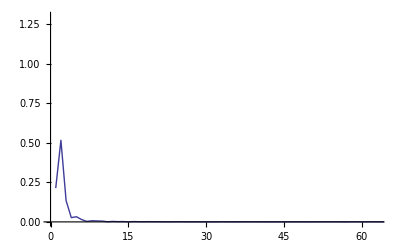

```mathematica
ListLinePlot[Abs[Fourier[ListConvolve[makefilters[32,125,500][[1]],noise,1]]],PlotRange->{{0,63},{0,1.3}}]
```

```mathematica
ListConvolve[makefilters[32,125,500][[15]],noise]
```

{0.0183728}

```mathematica
makefilters[2,125,500][[2]]
```

{-2.89219×10^-17,-0.00521819,8.57795×10^-17,0.00539508,-4.83979×10^-17,-0.00558438,2.92363×10^-17,0.00578745,-2.88753×10^-17,-0.00600585,-3.60059×10^-17,0.00624137,-5.14637×10^-17,-0.00649612,2.92363×10^-17,0.00677255,-2.88126×10^-17,-0.00707355,1.06341×10^-16,0.00740256,-5.56976×10^-17,-0.00776366,2.92363×10^-17,0.00816179,-2.87234×10^-17,-0.00860297,2.92363×10^-17,0.00909457,4.59767×10^-18,-0.00964575,2.92363×10^-17,0.0102681,-2.85866×10^-17,-0.0109762,2.92363×10^-17,0.0117893,1.50081×10^-17,-0.0127324,2.92363×10^-17,0.0138396,-2.83503×10^-17,-0.0151576,2.92363×10^-17,0.0167532,3.25942×10^-18,-0.0187241,2.92363×10^-17,0.0212207,1.25439×10^-17,-0.0244854,2.92363×10^-17,0.0289373,-2.72872×10^-17,-0.0353678,2.92363×10^-17,0.0454728,-2.59878×10^-17,-0.063662,2.92363×10^-17,0.106103,-1.94909×10^-17,-0.31831,0.5,-0.31831,-1.94909×10^-17,0.106103,2.92363×10^-17,-0.063662,-2.59878×10^-17,0.0454728,2.92363×10^-17,-0.0353678,-2.72872×10^-17,0.0289373,2.92363×10^-17,-0.0244854,1.25439×10^-17,0.0212207,2.92363×10^-17,-0.0187241,3.25942×10^-18,0.0167532,2.92363×10^-17,-0.0151576,-2.83503×10^-17,0.0138396,2.92363×10^-17,-0.0127324,1.50081×10^-17,0.0117893,2.92363×10^-17,-0.0109762,-2.85866×10^-17,0.0102681,2.92363×10^-17,-0.00964575,4.59767×10^-18,0.00909457,2.92363×10^-17,-0.00860297,-2.87234×10^-17,0.00816179,2.92363×10^-17,-0.00776366,-5.56976×10^-17,0.00740256,1.06341×10^-16,-0.00707355,-2.88126×10^-17,0.00677255,2.92363×10^-17,-0.00649612,-5.14637×10^-17,0.00624137,-3.60059×10^-17,-0.00600585,-2.88753×10^-17,0.00578745,2.92363×10^-17,-0.00558438,-4.83979×10^-17,0.00539508,8.57795×10^-17,-0.00521819,-2.89219×10^-17}